```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\jitter

```mathematica
data=Import["low_jitter.csv"];
```

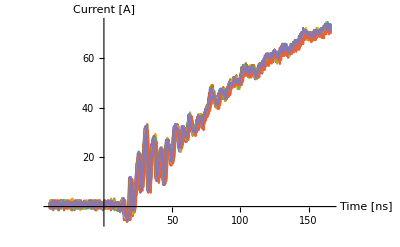

```mathematica
ListLinePlot[Table[
Thread[{data⟦All,1⟧,data⟦All,j⟧
}],{j,2,21}],PlotStyle->Automatic,
TicksStyle->Directive[Black,FontSize->fontsize,FontFamily->"Helvetica"],
AxesStyle->{{Black,Thick},{Black,Thick}},
AxesLabel->{Style["Time [ns]",Black,FontSize->fontsize],Style["Current [A]",Black,FontSize->fontsize]},
Ticks->{
{{5.*^-8,50,tick,Directive[Thick]},
{1*^-7,100,tick,Directive[Thick]},
{1.5*^-7,150,tick,Directive[Thick]}},
{{2,20,tick,Directive[Thick]},{4,40,tick,Directive[Thick]},{6,60,tick,Directive[Thick]}}
},ImageSize->Full]
```

```mathematica
tick=0.04;fontsize=44;
```

```mathematica
Quantity[5*^-8,"Seconds"]
```

1/20000000 s